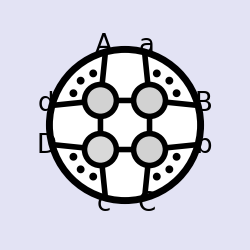
-Graphics-
One-Loop Amplitude Integrands
and Integrals in N=4 SYM
Jacob L. Bourjaily, 2013

```mathematica
<<loop_amplitudes.m
```

```mathematica
capexpand = {ab[x___, cap[{a_, b_}, {c__}], y___] :> ab[b, c] ab[x, a, y] + ab[c, a] ab[x, b, y],
               ab[x___,cap1[{a_,b_},{c__},{d__}],y___]:>(-1)^Length[{y}](ab[x,y,a,c]ab[x,y,b,d]-ab[x,y,a,d]ab[x,y,b,c])};
sortab={i_ab:>ordercup[i]Signature[i]/Signature[ordercup[i]]};
ordercup[exp_]:=SortBy[exp,Which[Head[#]===cap,1.5,Head[#]===shift,1.4,True,#]&];
shifexp={ab[x___,shift[y_,z_],w___]:>ab[x,y⟦1⟧,w]+z ab[x,y⟦2⟧,w]};
mom=RandomInteger[{-100,100},{20,4}];
mom1=Table[Binomial[n+i,i],{n,20},{i,0,3}];
neab[exp_]:=exp/.shifexp//.capexpand/.ab[x__]:>Det[mom[[{x}]]];
neab1[exp_]:=exp/.shifexp//.capexpand/.ab[x__]:>Det[mom1[[{x}]]];
randomPositiveZs[n_]:=(Zs=Nest[Function[{mat},Block[{hatted=Append[(Append[Total[mat⟦#1;;-1⟧],1]&)/@Range[2,Length[mat]],Append[PadRight[{},Length[mat⟦1⟧]],1]],newRow=RandomInteger[{1,10},{Length[mat]}]},newRow hatted]],RandomInteger[{1,10},{n+8,1}],3];Zs=Transpose[Inverse[Transpose[Zs⟦{1,2,3,4}⟧]].Transpose[Zs]]⟦5;;-1⟧;)
neabp[exp_]:=exp/.shifexp//.capexpand/.ab[x__]:>Det[Zs⟦{x}⟧];
```

```mathematica
dabtoeta=dab[x__]:>Apply[ab,Partition[{x},4,1,5],{1}].η/@{x};
abfactor[exp_]:=Module[{lis=Union@@Cases[exp//.shifexp//.capexpand,_ab,Infinity]/.ab->List},If[Position[exp/(ab@@@Subsets[lis,{4}])//neab,_Integer]=!={},ab@@@Subsets[lis,{4}][[Flatten[Position[exp/(ab@@@Subsets[lis,{4}])//neab,_Integer]]]],exp]];
ordercup2[exp_]:=SortBy[exp,If[Head[#]===cap,If[(#/.cap:>List)[[1]]=={8,9},10,0.5], #]&];

sortR2={i_R:>ordercup2[i]Signature[i]/Signature[ordercup2[i]]};
repR1={R[cap[{a_,b_},{c_,n,n+1}],x___,a_,y___,cap[{n,n+1},m__]]:>(ab[a,b,n,n+1]ab[c,x,a,y])/ab[x,a,y,cap[{n,n+1},{a,b,c}]] R[c,cap[{a,b},{c,n,n+1}],x,a,y]R[a,b,c,n,n+1],R[cap[{b_,a_},{c_,n,n+1}],x___,a_,y___,cap[{n,n+1},m__]]:>(ab[a,b,n,n+1]ab[c,x,a,y])/ab[x,a,y,cap[{n,n+1},{a,b,c}]] R[c,cap[{a,b},{c,n,n+1}],x,a,y]R[a,b,c,n,n+1]};
repR2={R[cap[{a___},{c_,n,n+1}],d___,n+1,cap[{n,n+1},m__]]:>(ab[c,d,n+1]ab[a,n,n+1])/(ab[c,a,n+1]ab[d,n,n+1])R[c,cap[{a},{c,n,n+1}],d,n]R[a,c,n,n+1]};
qlogtodabm={Qlog[ab[7,8,1,i_]/ab[7,8,1,j_]]:>dab[1,i,j,n-1,n]/(ab[1,i,n-1,n] ab[1,j,n-1,n])};
numabfactor[exp_]:=ab@@@Subsets[Range[9],{4}][[Flatten[Position[exp/(ab@@@Subsets[Range[9],{4}])//neab,_Integer]]]];
dabsimp[exp_]:=Module[{f1,f2,f3},f1=exp/.dabcapexpand/.dabtoeta//neab//Simplify;
f2=dab@@(Cases[f1,η[_],Infinity]/.η->List//Flatten);
f3=Times@@(exp/f2/.dabcapexpand/.dabtoeta//neab//Simplify//numabfactor);
If[Abs[( exp/(f2*f3)/.dabcapexpand/.dabtoeta//neab//Simplify)/.i_η:>1//neab]<10,f2*f3 ( exp/(f2*f3)/.dabcapexpand/.dabtoeta//neab//Simplify)/.sortall,exp]
];

absim[exp_]:=Module[{f1},f1=Times@@(exp//numabfactor);
If[Abs[exp/f1//neab]<10,f1(exp/f1//neab),exp]
];
```

```mathematica
u2ab2[a_,b_]:={ξ:>(ab[1,cap1[{n,2},{b-1,b},{c-1,c}]]ab[2,3,n-1,n])/(ab[1,2,3,n]ab[1,2,c-1,c]ab[b-1,b,n-1,n]),Subscript[τ, v]:>-(ab[1,2,3,n]ab[a-1,a,n-1,n])/(ab[2,3,n-1,n]ab[1,a-1,a,n]),u:>(ab[n,1,a-1,a]ab[b-1,b,n-2,n-1])/(ab[n,1,b-1,b]ab[a-1,a,n-2,n-1]),v:>(ab[a-1,a,b-1,b]ab[n,1,n-2,n-1])/(ab[n,1,b-1,b]ab[a-1,a,n-2,n-1]),z:>1/2(1+u-v+Sqrt[(1-u-v)^2-4u v]),zb:>1/2(1+u-v-Sqrt[(1-u-v)^2-4u v])};
```

```mathematica
tautot3={τ->(t σ-u (v+σ))/(t^2+u+t (-1-u+v))};
```

```mathematica
yitoab={Subscript[y, 1]:>1-(ab[1,6,7,8] ab[2,3,4,5])/(ab[1,4,5,8] ab[2,3,6,7])-(ab[1,2,3,8] ab[4,5,6,7])/(ab[1,4,5,8] ab[2,3,6,7]),Subscript[y, 2]:>(ab[1,6,7,8] ab[2,3,4,5])/(ab[1,4,5,8] ab[2,3,6,7])(ab[1,2,3,8] ab[4,5,6,7])/(ab[1,4,5,8] ab[2,3,6,7]),σ:>(ab[1,2,3,8] (ab[2,3,7,cap[{4,5},{6,7,8}]]))/(ab[2,3,7,8] ab[1,4,5,8] ab[2,3,6,7])};
taure3={τ->(t σ-u (v+σ))/(t^2+u+t (-1-u+v))};
```

```mathematica
u2ab2[a_,b_]=With[{n=8},{σ:>(ab[1,a-1,a,n] (ab[a-1,a,n-1,cap[{b-1,b},{n-2,n-1,n}]]))/(ab[a-1,a,n-1,n] ab[1,b-1,b,n] ab[a-1,a,n-2,n-1]),Subscript[τ, v]:>-(ab[1,2,3,n]ab[a-1,a,n-1,n])/(ab[2,3,n-1,n]ab[1,a-1,a,n]),u:>(ab[n,1,a-1,a]ab[b-1,b,n-2,n-1])/(ab[n,1,b-1,b]ab[a-1,a,n-2,n-1]),v:>(ab[a-1,a,b-1,b]ab[n,1,n-2,n-1])/(ab[n,1,b-1,b]ab[a-1,a,n-2,n-1]),z:>1/2(1+u-v+Sqrt[(1-u-v)^2-4u v]),zb:>1/2(1+u-v-Sqrt[(1-u-v)^2-4u v])}];
```

```mathematica
((ab[1,2,3,8] (ab[2,3,7,cap[{4,5},{6,7,8}]]))/(ab[2,3,7,8] ab[1,4,5,8] ab[2,3,6,7]))/u/.u2ab2[3,5]/.sortab
```

-(ab[1,2,3,8] ab[1,4,5,9] ab[cap[{4,5},{6,7,8}],2,3,7])/(ab[1,2,3,9] ab[1,4,5,8] ab[2,3,6,7] ab[4,5,7,8])

```mathematica
(ab[1,a-1,a,n] (ab[a-1,a,n-1,cap[{b-1,b},{n-2,n-1,n}]]))/(ab[a-1,a,n-1,n] ab[1,b-1,b,n] ab[a-1,a,n-2,n-1])
```

```mathematica
randomPositiveZs[20];
```

```mathematica
Limit[-(4 ab[3,4,5,6] ab[5,6,7,8] ab[7,8,9,10] ab[9,10,3,4])/(ab[3,4,7,8]^2 ab[5,6,9,10]^2)+(1-(ab[3,4,5,6] ab[7,8,9,10])/(ab[3,4,7,8] ab[5,6,9,10])-(ab[5,6,7,8] ab[9,10,3,4])/(ab[3,4,7,8] ab[5,6,9,10]))^2//fullabB//neabp,e->0]/.τ:>-(Subscript[τ, v](t σ-u (v+σ)))/(t^2+u+t (-1-u+v))/.u2ab2[4,6]//neabp//Factor
```

((31972509344977948269-197153319280301474832 t+57341725055234224619840 t^2)^2)/(93548122739853376 (-77571+690536 t)^2 (1007757+305856376 t)^2)

```mathematica
Limit[(σ+√(σ^2+Δ τ^2+2 σ τ Subscript[y, 1]-4 τ Subscript[y, 2]))/τ,τ->Infinity]
```

√Δ

```mathematica
(σ+√(σ^2+Δ τ^2+2 σ τ Subscript[y, 1]-4 τ Subscript[y, 2]))/τ/.Δ->Sqrt[Subscript[y, 1]^2-4 Subscript[y, 2]]/.yitoab//neabp
```

(19781469000/2473369001831+√(391306515797961000000/6117554219218477281352561+(44650442823344400 τ)/3639566372917033663+(√4477967948566641 τ^2)/72103577))/τ

```mathematica
Solve[{u==z zb,v==(1-z)(1-zb)},{z,zb}]
```

{{z→1/2 (1+u-√(-4 u+(1+u-v)^2)-v),zb→1/2 (1+u+√(-4 u+(1+u-v)^2)-v)},{z→1/2 (1+u+√(-4 u+(1+u-v)^2)-v),zb→1/2 (1+u-√(-4 u+(1+u-v)^2)-v)}}

```mathematica
Solve[tp==1/2(1+u-v+t),t]
```

{{t→-1+2 tp-u+v}}

```mathematica
(2 (t σ+σ Subscript[y, 1]-2 Subscript[y, 2]))/(t^2-((1-u-v)^2-4u v))/.{Subscript[y, 1]:>1-u-v,Subscript[y, 2]:>u v}/.t->-1+2 tp-u+v/.{σ:>-1+1/vn,u:>u1,v:>v1}//Simplify
```

```mathematica
(tp-tp vn+u1 (-1+vn-v1 vn))/((tp^2+u1+tp (-1-u1+v1)) vn)/.tp->(-t+vn-v1 vn)/vn//Simplify
```

(t (-1+vn)-vn (-1+u1+v1+vn+u1 (-1+v1) vn-v1 vn))/(t^2+t (-1+u1+v1) vn+u1 v1 vn^2)

```mathematica
Solve[vn(1-v1-tp)==t,tp]
```

{{tp→(-t+vn-v1 vn)/vn}}

```mathematica
Solve[t^2+t (-1+u1+v1) vn+u1 v1 vn^2==0,t]
```

{{t→1/2 (vn-u1 vn-v1 vn-√(1-2 u1+u1^2-2 v1-2 u1 v1+v1^2) vn)},{t→1/2 (vn-u1 vn-v1 vn+√(1-2 u1+u1^2-2 v1-2 u1 v1+v1^2) vn)}}

```mathematica
(tp σ-u (v+σ))/(tp^2+u+tp (-1-u+v))/.tp->t
```

```mathematica
(t σ-u (v+σ))/(t^2+u+t (-1-u+v))/.{σ:>-1+1/vn,u:>u1,v:>v1}//Factor
```

-(-t+u1+t vn-u1 vn+u1 v1 vn)/((-t+t^2+u1-t u1+t v1) vn)

```mathematica
σ/.yitoab
```

(ab[1,2,3,8] ab[2,3,7,cap[{4,5},{6,7,8}]])/(ab[1,4,5,8] ab[2,3,6,7] ab[2,3,7,8])

```mathematica
Solve[(tp σ-u (4 v+σ))/(tp^2+u+tp (-1-u+v))==τ,tp]
```

{{tp→(σ+τ+u τ-v τ-√(4 τ (-4 u v-u σ-u τ)+(σ+τ+u τ-v τ)^2))/(2 τ)},{tp→(σ+τ+u τ-v τ+√(4 τ (-4 u v-u σ-u τ)+(σ+τ+u τ-v τ)^2))/(2 τ)}}

```mathematica
Limit[(σ+τ+u τ-v τ+√(4 τ (-4 u v-u σ-u τ)+(σ+τ+u τ-v τ)^2))/(2 τ),τ->Infinity]
```

```mathematica
(t-1/2 (1+u-v+√(u^2+(-1+v)^2-2 u (1+v))))(t-1/2 (1+u-v-√(u^2+(-1+v)^2-2 u (1+v))))//Simplify
```

t^2+u+t (-1-u+v)

```mathematica
scalarBoxIntegral[{{4,5},{6,7},{8,9},{10,1,2,3}}]
```

-Li[1]+Li[1/2 (1+(ab[3,4,5,6] ab[7,8,9,10])/(ab[3,4,7,8] ab[5,6,9,10])-(ab[5,6,7,8] ab[9,10,3,4])/(ab[3,4,7,8] ab[5,6,9,10])+√(-(4 ab[3,4,5,6] ab[5,6,7,8] ab[7,8,9,10] ab[9,10,3,4])/(ab[3,4,7,8]^2 ab[5,6,9,10]^2)+(1-(ab[3,4,5,6] ab[7,8,9,10])/(ab[3,4,7,8] ab[5,6,9,10])-(ab[5,6,7,8] ab[9,10,3,4])/(ab[3,4,7,8] ab[5,6,9,10]))^2))]+Li[1/2 (1-(ab[3,4,5,6] ab[7,8,9,10])/(ab[3,4,7,8] ab[5,6,9,10])+(ab[5,6,7,8] ab[9,10,3,4])/(ab[3,4,7,8] ab[5,6,9,10])+√(-(4 ab[3,4,5,6] ab[5,6,7,8] ab[7,8,9,10] ab[9,10,3,4])/(ab[3,4,7,8]^2 ab[5,6,9,10]^2)+(1-(ab[3,4,5,6] ab[7,8,9,10])/(ab[3,4,7,8] ab[5,6,9,10])-(ab[5,6,7,8] ab[9,10,3,4])/(ab[3,4,7,8] ab[5,6,9,10]))^2))]+1/2 log[(ab[3,4,5,6] ab[7,8,9,10])/(ab[3,4,7,8] ab[5,6,9,10])] log[(ab[5,6,7,8] ab[9,10,3,4])/(ab[3,4,7,8] ab[5,6,9,10])]-log[1/2 (1+(ab[3,4,5,6] ab[7,8,9,10])/(ab[3,4,7,8] ab[5,6,9,10])-(ab[5,6,7,8] ab[9,10,3,4])/(ab[3,4,7,8] ab[5,6,9,10])+√(-(4 ab[3,4,5,6] ab[5,6,7,8] ab[7,8,9,10] ab[9,10,3,4])/(ab[3,4,7,8]^2 ab[5,6,9,10]^2)+(1-(ab[3,4,5,6] ab[7,8,9,10])/(ab[3,4,7,8] ab[5,6,9,10])-(ab[5,6,7,8] ab[9,10,3,4])/(ab[3,4,7,8] ab[5,6,9,10]))^2))] log[1/2 (1-(ab[3,4,5,6] ab[7,8,9,10])/(ab[3,4,7,8] ab[5,6,9,10])+(ab[5,6,7,8] ab[9,10,3,4])/(ab[3,4,7,8] ab[5,6,9,10])+√(-(4 ab[3,4,5,6] ab[5,6,7,8] ab[7,8,9,10] ab[9,10,3,4])/(ab[3,4,7,8]^2 ab[5,6,9,10]^2)+(1-(ab[3,4,5,6] ab[7,8,9,10])/(ab[3,4,7,8] ab[5,6,9,10])-(ab[5,6,7,8] ab[9,10,3,4])/(ab[3,4,7,8] ab[5,6,9,10]))^2))]

```mathematica
Limit[(ab[4,5,6,7] ab[9,10,2,3])/(ab[2,3,6,7] ab[4,5,9,10])//fullabB,e->0]//Factor
```

((1+τ) ab[1,2,3,9] ab[2,3,8,9] ab[4,5,6,7])/(ab[2,3,6,7] (τ ab[1,4,5,9] ab[2,3,8,9]+ab[1,2,3,9] ab[4,5,8,9]))

```mathematica
((ab[1,2,3,8] (ab[2,3,7,cap[{4,5},{6,7,8}]]))/(ab[2,3,7,8] ab[1,4,5,8] ab[2,3,6,7]))/u/.u2ab2[3,5]/.sortab//neabp
```

201375/274424

```mathematica
ab[cap[{6,8},{4,7,5}],2,3,7]/(ab[2,3,7,8] ab[4,5,6,7])//.capexpand/.sortab//Expand
```

```mathematica
-1+1/vn
```

```mathematica
u
```

```mathematica
(u (v+σ))/σ
```

```mathematica
(u (v+σ))/σ/.u2ab2[3,5]/.sortab//Factor
```

-(ab[4,5,6,7] (ab[1,6,7,8] ab[2,3,4,5] ab[2,3,7,8]-ab[1,2,3,8] ab[cap[{4,5},{6,7,8}],2,3,7]))/(ab[1,4,5,8] ab[2,3,6,7] ab[cap[{4,5},{6,7,8}],2,3,7])

```mathematica
(ab[1,6,7,8] ab[2,3,4,5] ab[2,3,7,8]-ab[1,2,3,8] ab[cap[{4,5},{6,7,8}],2,3,7])//abfactor
```

ab[1,6,7,8] ab[2,3,4,5] ab[2,3,7,8]-ab[1,2,3,8] ab[cap[{4,5},{6,7,8}],2,3,7]

```mathematica
-(4 ab[3,4,5,6] ab[5,6,7,8] ab[7,8,9,10] ab[9,10,3,4])/(ab[3,4,7,8]^2 ab[5,6,9,10]^2)+(1-(ab[3,4,5,6] ab[7,8,9,10])/(ab[3,4,7,8] ab[5,6,9,10])-(ab[5,6,7,8] ab[9,10,3,4])/(ab[3,4,7,8] ab[5,6,9,10]))^2
```

```mathematica
Limit[(ab[5,6,7,8] ab[9,10,3,4])/(ab[3,4,7,8] ab[5,6,9,10])//fullabB//neabp,e->0]//Simplify
```

```mathematica
Solve[(1521 (14076+39281 τ))/(1064 (179124+48580571 τ))==0,τ]
```

{{τ→-14076/39281}}

```mathematica
Limit[(-(4 ab[3,4,5,6] ab[5,6,7,8] ab[7,8,9,10] ab[9,10,3,4])/(ab[3,4,7,8]^2 ab[5,6,9,10]^2)+(1-(ab[3,4,5,6] ab[7,8,9,10])/(ab[3,4,7,8] ab[5,6,9,10])-(ab[5,6,7,8] ab[9,10,3,4])/(ab[3,4,7,8] ab[5,6,9,10]))^2)//fullabB//neabp,e->0]//Simplify
```

```mathematica
(28621310725155600+17371805833955085864 τ+2641897187180084448745 τ^2)/(1132096 (179124+48580571 τ)^2)/.τ->-(828 (770998857135+41216 t) (12866201789645+700672 t))/(39281 (-594426867115519000967625+1698758656 t^2))//Factor
```

((771957870991681172663286422100228375+82535384633553765394034910720 t+2206108417975667064832 t^2)^2)/(4528384 (772791249165+41216 t)^2 (472600623564881635785+25266600708608 t)^2)

```mathematica
Solve[(225 (28621310725155600+17371805833955085864 τ+2641897187180084448745 τ^2))/1698758656==(58439660312115/8798944+t(τ+14076/39281))^2,τ]//Factor
```

{{τ→-14076/39281},{τ→-(828 (770998857135+41216 t) (12866201789645+700672 t))/(39281 (-594426867115519000967625+1698758656 t^2))}}

```mathematica
Sqrt[3415193897395389059215773225/77421415515136]
```

58439660312115/8798944

```mathematica
(225 (28621310725155600+17371805833955085864 τ+2641897187180084448745 τ^2))/1698758656、。-(828 (770998857135+41216 t) (12866201789645+700672 t))/(39281 (-594426867115519000967625+1698758656 t^2))
```

```mathematica
Solve[τ==-(828 (770998857135+41216 t) (12866201789645+700672 t))/(39281 (-594426867115519000967625+1698758656 t^2)),t]
```

{{t→(15 (-716859833161944-39281 √(28621310725155600+17371805833955085864 τ+2641897187180084448745 τ^2)))/(41216 (14076+39281 τ))},{t→(15 (-716859833161944+39281 √(28621310725155600+17371805833955085864 τ+2641897187180084448745 τ^2)))/(41216 (14076+39281 τ))}}

```mathematica
Limit[(15 (-716859833161944+39281 √(28621310725155600+17371805833955085864 τ+2641897187180084448745 τ^2)))/(41216 (14076+39281 τ)),τ->Infinity]
```

(2535 √92500164111203545)/41216

```mathematica
u2ab2[a_,b_]=With[{n=9},{vn:>(ab[b-1,b,n-2,n-1]ab[a-1,a,n-1,n])/(ab[a-1,a,n-2,n-1]ab[b-1,b,n-1,n]),Subscript[τ, v]:>-(ab[1,2,3,n]ab[a-1,a,n-1,n])/(ab[2,3,n-1,n]ab[1,a-1,a,n]),u1:>(ab[n,1,a-1,a]ab[b-1,b,n-2,n-1])/(ab[n,1,b-1,b]ab[a-1,a,n-2,n-1]),v1:>(ab[a-1,a,b-1,b]ab[n,1,n-2,n-1])/(ab[n,1,b-1,b]ab[a-1,a,n-2,n-1]),z:>1/2(1+u-v+Sqrt[(1-u-v)^2-4u v]),zb:>1/2(1+u-v-Sqrt[(1-u-v)^2-4u v])}];
```

```mathematica
-Subscript[τ, v] ((t-u1(1-un-deln))(t-u1(1-un+deln)))/((t-vn(1-v1-del1))(t-vn(1-v1+del1)))/.deln:>1-vn/.un:>0/.del1:>Sqrt[(1-u1-v1)^2-4u1 v1]/.u2ab2[4,6]//neabp//Simplify
```

```mathematica
(28621310725155600+17371805833955085864 τ+2641897187180084448745 τ^2)/(1132096 (179124+48580571 τ)^2)/.τ:>-(14076 (-41893218639+19200439859776 t) (-2493054369+19200439859776 t))/(3571 (118756492591417023489705-907028342219188652906177280 t+4055225798897625247970471936 t^2))//Simplify
```

((9369916874622773540949098935935-125451012392517533970253404523033728 t+478759632679802817215641160100374966272 t^2)^2)/(4528384 (4115230934055113787459516621+2349440752380951187351665784512 t-225997342258946616044120460571353088 t^2)^2)

```mathematica
Solve[τ==-(14076 (-41893218639+19200439859776 t) (-2493054369+19200439859776 t))/(3571 (118756492591417023489705-907028342219188652906177280 t+4055225798897625247970471936 t^2)),t]
```

{{t→(1639089 (190587936+51459670210 τ-√(28621310725155600+17371805833955085864 τ+2641897187180084448745 τ^2)))/(19200439859776 (14076+39281 τ))},{t→(1639089 (190587936+51459670210 τ+√(28621310725155600+17371805833955085864 τ+2641897187180084448745 τ^2)))/(19200439859776 (14076+39281 τ))}}

```mathematica
Limit[(1639089 (190587936+51459670210 τ+√(28621310725155600+17371805833955085864 τ+2641897187180084448745 τ^2)))/(19200439859776 (14076+39281 τ)),τ->Infinity]
```

(459 (51459670210+169 √92500164111203545))/211204838457536